```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory [NotebookDirectory[]];
Get["mcc.m"]
```

Približna vrednost števila π: 3.1476

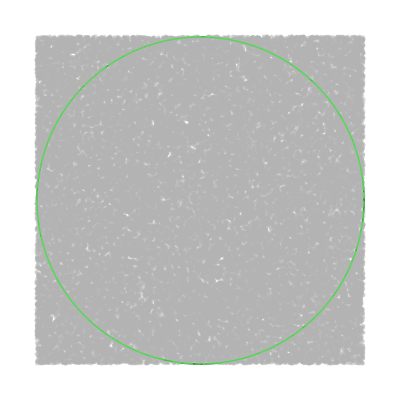

```mathematica
n=50000; 
Aproksimacija=MonteCarlo[n];

Print["Približna vrednost števila π: ",N[Aproksimacija]]
Graphics[{Circle[],PointSize[Small], GrayLevel[0.7,0.54],Point[RandomReal[{-1,1},{n,2}]],Green,Circle[{0,0},1]}]
```